```mathematica
s=NDSolve[{x''[t]+Sin[x[t]]==0,x[0]==0,x'[0]==1.98},x[t],{t,0,20}]
```

{{x[t]→InterpolatingFunction[{{0.,20.}},<>][t]}}

```mathematica
tf=(t/.FindRoot[Evaluate[x[t]/.s]==0,{t,15}])
```

13.4264

```mathematica
c1=NIntegrate[Evaluate[x[t]/.s]Sin[2Pi t/tf],{t,0,tf}]/Integrate[Sin[2Pi t/tf]^2,{t,0,tf}]
```

{3.11152}

```mathematica
c2=NIntegrate[Evaluate[x[t]/.s]Sin[6Pi t/tf],{t,0,tf}]/Integrate[Sin[6Pi t/tf]^2,{t,0,tf}]
```

{0.287266}

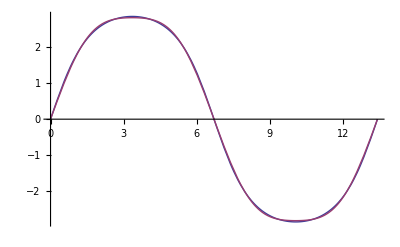

```mathematica
Plot[{x[t]/.s,c1 Sin[2Pi t/tf]+c2 Sin[6Pi t/tf]},{t,0,tf},PlotRange->All]
```